```mathematica
info=Import["C:\\Users\\Ксения\\Documents\\Магистратура\\Геномика\\out.dat","Table"][[1]];
l=Length[info]/3;realPi={};vitPi={};prob={};
(*realPi ={pi[[1]]};vitPi={pi[[l+1]]};*)
For[i=1,i≤l,i++,AppendTo[realPi,info[[i]]];AppendTo[vitPi,info[[i+l]]];AppendTo[prob,info[[i+2l]]]]
```

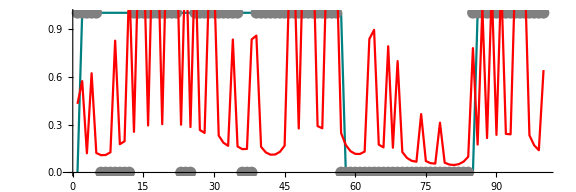

```mathematica
Show[ListPlot[vitPi,PlotStyle->{RGBColor[0,0.5,0.5]},Joined->True,AspectRatio->1/3],ListPlot[realPi,PlotStyle->{Gray},PlotMarkers->{Automatic,12},AspectRatio->1/3],ListPlot[prob,PlotStyle->{Red},Joined->True,AspectRatio->1/3],ImageSize->Large,AxesStyle->Black]
```